## functions

```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
MinutesSinceMidnightToHourMinute[minutesSinceMidnight_]:={
IntegerPart[minutesSinceMidnight/60],
60(minutesSinceMidnight/60-IntegerPart[minutesSinceMidnight/60])
}
```

## k vals for rooms

```mathematica
roomNames={"ovi","PK","SZGK","Gólya","Mérce","vendégtér","kisterem","Trafóház","Oktopusz 1"}
```

{ovi,PK,SZGK,Gólya,Mérce,vendégtér,kisterem,Trafóház,Oktopusz 1}

```mathematica
Solve[ΔT==Te+ΔT Exp[-Δt/tau],tau]
```

{{tau→ConditionalExpression[Δt/(2 ⅈ π C[1]+Log[ΔT/(-Te+ΔT)]), C[1]∈ℤ]}}

```mathematica
1-Te/ΔT==ΔT/(ΔT-Te)
```

1-Te/ΔT==ΔT/(-Te+ΔT)

```mathematica
dayDirectories=Drop[FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\raw\\"],12]
```

{C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-18,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-19,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-20,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-21,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-22,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-23,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-24,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-25,C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26}

```mathematica
pumpStates=Table[Flatten[Table[
Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]]+24 60 (day-1),
#[[3]]
}&,Select[Import[dayDirectories[[day]]<>"//pump_states.csv"],#[[2]]==pump&]]
,{day,1,Length[dayDirectories]}],1],{pump,1,4}];
```

```mathematica
externalTemp=Flatten[Table[
Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]]+24 60 (day-1),
#[[2]]
}&,Import[dayDirectories[[day]]<>"//external_temp.csv"]]
,{day,1,Length[dayDirectories]}],1];
```

```mathematica
minuteStep=5;
externalTempInterpolated=Select[Quiet[Table[
{minute,Module[
{externalTempPrecedingPos,externalTempPrecedingTime,externalTempPrecedingVal,externalTempSucceedingTime,externalTempSucceedingVal},
externalTempPrecedingPos=Min[Length[externalTemp]-1,PrecedingPos[Transpose[externalTemp][[1]],minute]];
externalTempPrecedingTime=externalTemp[[externalTempPrecedingPos]][[1]];
externalTempPrecedingVal=externalTemp[[externalTempPrecedingPos]][[2]];
externalTempSucceedingTime=externalTemp[[externalTempPrecedingPos+1]][[1]];
externalTempSucceedingVal=externalTemp[[externalTempPrecedingPos+1]][[2]];
externalTempPrecedingVal+(externalTempSucceedingVal-externalTempPrecedingVal)((minute-externalTempPrecedingTime)/(externalTempSucceedingTime-externalTempPrecedingTime))
]}
,{minute,0,Length[dayDirectories]24 60,minuteStep}]],NumberQ[Total[#]]&];
```

```mathematica
roomTempsRaw=Table[Flatten[
Table[
Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]]+24 60 (day-1),
#[[3]]
}&,Select[Import[dayDirectories[[day]]<>"//measured_temps.csv"],#[[2]]==room&]]
,{day,1,Length[dayDirectories]}]
,1],{room,1,9}];
```

```mathematica
roomTempsLateReadingsFiltered=ParallelTable[Table[
If[
60<roomTempsRaw[[room]][[n]][[1]]-roomTempsRaw[[room]][[n-1]][[1]],
Nothing,
roomTempsRaw[[room]][[n]]
]
,{n,2,Length[roomTempsRaw[[room]]]}],{room,1,9}];
```

```mathematica
ListPlot[roomTempsLateReadingsFiltered,Joined->True]
```

```mathematica
timeStep=5;
timeWindow=60;
roomTempsLateReadingsFilteredDenoised=ParallelTable[Table[
Select[
roomTempsLateReadingsFiltered[[room]],
Between[#[[1]],{time-timeWindow/2,time+timeWindow/2}]&
]//If[#!={},Mean[#],Nothing]&
,{time,0,Length[dayDirectories]24 60,timeStep}],{room,1,9}];
```

```mathematica
ListPlot[roomTempsLateReadingsFilteredDenoised[[room]],Joined->False]
```

```mathematica
kValData=Table[GatherBy[Select[Quiet[Table[
Module[
{time,temp,precedingTime,precedingTemp},
time=roomTempsLateReadingsFilteredDenoised[[room]][[n]][[1]];
temp=roomTempsLateReadingsFilteredDenoised[[room]][[n]][[2]];
precedingTime=roomTempsLateReadingsFilteredDenoised[[room]][[n-1]][[1]];
precedingTemp=roomTempsLateReadingsFilteredDenoised[[room]][[n-1]][[2]];
If[
pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],time]]][[2]]==pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],precedingTime]]][[2]],
{
pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],time]]][[2]],
time-precedingTime,
temp-precedingTemp,
If[
pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],time]]][[2]]==1,
40,
externalTempInterpolated[[PrecedingPos[Transpose[externalTempInterpolated][[1]],time]]][[2]]
],
temp
},
Nothing
]//N
],
{n,2,Length[roomTempsLateReadingsFilteredDenoised[[room]]]}]],NumberQ[Total[#]]&],First],{room,1,9}];
```

```mathematica
kPoints=Quiet[Table[Table[
Select[Quiet[Map[
{#[[4]]-#[[5]],#[[3]]/(#[[2]]/60)}
&,kValData[[room]][[heatingOnOff]]]],NumberQ[Total[#]]&&Between[#[[2]],{-1500,1500}]&],{heatingOnOff,1,2}],{room,1,9}]];
```

```mathematica
kFits=Quiet[Table[Table[Fit[kPoints[[room]][[heatingOnOff]],{1,x},x],{heatingOnOff,1,2}],{room,1,9}]];
kFits//Grid
```

```mathematica
kEstimates1=Quiet[Table[Table[kFits[[room]][[heatingOnOff]][[2]][[1]],{heatingOnOff,1,2}],{room,1,9}]]
```

{{0.226563,0.034269},{0.360309,0.0577719},{-0.020361,0.30552},{0.450054,-0.00920171},{-0.0667763,-0.436619},{-0.0197675,0.00867145},{0.359395,0.00608431},{0.,1},{0.46566,0.0306584}}

```mathematica
Quiet[Table[
Show[{
ListPlot[
kPoints[[room]],
PlotStyle->{Red,Blue},PlotLabel->roomNames[[room]],ImageSize->200,AspectRatio->1
],
Plot[
{kFits[[room]][[1]],kFits[[room]][[2]]},{x,-100,100},
PlotStyle->{Red,Blue}
]
}],{room,{1,2,3,4,5,6,7,9}}]]//ArrayReshape[#,{2,5},""]&//Grid
```

```mathematica
kEstimates2=Quiet[Table[Table[
Mean[Select[Quiet[Map[
(#[[3]]/(#[[2]]/60))/(#[[4]]-#[[5]])
&,kValData[[room]][[heatingOnOff]]]],NumberQ[Total[#]]&]]
,{heatingOnOff,{1,2}}],{room,1,9}]];
```

```mathematica
Reverse[SortBy[Table[
Flatten[{
roomNames[[room]],
kEstimates1[[room]]
}]
,{room,{1,2,3,4,5,6,7,9}}],#[[3]]&]]//Grid
```

SZGK | -0.020361 | 0.30552
PK | 0.360309 | 0.0577719
ovi | 0.226563 | 0.034269
Oktopusz 1 | 0.46566 | 0.0306584
vendégtér | -0.0197675 | 0.00867145
kisterem | 0.359395 | 0.00608431
Gólya | 0.450054 | -0.00920171
Mérce | -0.0667763 | -0.436619

```mathematica
roomTempsLateReadingsFilteredDenoised[[1]]
```

{9}

```mathematica
kValData2=Table[
Table[
Transpose[Transpose[vals][[2;;3]]]
,{vals,GatherBy[Select[Quiet[Table[
Module[
{time,temp,precedingTime,precedingTemp},
time=roomTempsLateReadingsFilteredDenoised[[room]][[n]][[1]];
temp=roomTempsLateReadingsFilteredDenoised[[room]][[n]][[2]];
{
pumpStates[[roomToPump[[room]]]][[PrecedingPos[Transpose[pumpStates[[roomToPump[[room]]]]][[1]],time]]][[2]],
time,
temp
}//N
],
{n,2,Length[roomTempsLateReadingsFilteredDenoised[[room]]]}]],NumberQ[Total[#]]&],First]}]
,{room,1,9}];
```

```mathematica
heatingOnOff=1;(*N*)
```

```mathematica
heatingOnOff=2;(*OFF*)
```

```mathematica
ListPlot[kValData2[[room]][[heatingOnOff]]]
```

```mathematica
s=2.1;
k=-0.0065>>*;
```

```mathematica
Show[{
Plot[data[[1]][[2]]+s Exp[x k]-s,{x,0,500}],
ListPlot[data,Joined->True]
}]
```

```mathematica
Transpose[kEstimates1][[2]]
```

{0.034269,0.0577719,0.30552,-0.00920171,-0.436619,0.00867145,0.00608431,1,0.0306584}

```mathematica
Table[Show[{
Plot[data[[-1]][[2]]+s Exp[x Transpose[kEstimates1][[2]][[room]]],{x,0,500}],
ListPlot[data,Joined->True]
}],{room,{1,2,3,4,5,6,7,9}}]
```

```mathematica
Manipulate[Show[{
ListPlot[data,Joined->True],
Plot[data[[-1]][[2]]+s Exp[x k],{x,0,500}]
}],
{{k,0},-1/50,0,0.001},
{{s,1},1,5,0.01}
]
```

## formatting prototype

```mathematica
precedingDay="2023-11-25"
```

2023-11-25

```mathematica
day="2023-11-26"
```

2023-11-26

```mathematica
precedingDayRawDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\raw\\"<>precedingDay];
```

```mathematica
dayRawDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\raw\\"<>day];
dayRawDataFiles//Column
```

C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\albatros_state.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\external_temp.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\gas_pulse_times.txt
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\heatmeter_images
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\heatmeter_readouts.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\measured_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\pump_states.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-26\set_temps.csv

```mathematica
room=1;
```

```mathematica
roomTempsRaw=Join[
Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]]-24 60,
#[[3]]
}&,Select[Import[precedingDayRawDataFiles[[6]]],#[[2]]==room&]],
Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]],
#[[3]]
}&,Select[Import[dayRawDataFiles[[6]]],#[[2]]==room&]]
];
```

```mathematica
ListPlot[roomTempsRaw]
```

```mathematica
roomTempsLateReadingsFiltered//Length
```

298

```mathematica
roomTempsRaw//Length
```

300

```mathematica
lateTime=60 ;
roomTempsLateReadingsFiltered=Table[
If[
lateTime<roomTempsRaw[[n]][[1]]-roomTempsRaw[[n-1]][[1]]&&roomTempsRaw[[n]][[2]]==roomTempsRaw[[n-1]][[2]],
Nothing,
roomTempsRaw[[n]]
]
,{n,2,Length[roomTempsRaw]}];
```

```mathematica
ListPlot[roomTempsLateReadingsFiltered,Joined->True]
```

```mathematica
timeStep=5;
timeWindow=1 60;
roomTempsLateReadingsFilteredDenoised=Table[
Select[
roomTempsLateReadingsFiltered,
Between[#[[1]],{time-timeWindow/2,time+timeWindow/2}]&
]//If[#!={},Mean[#],Nothing]&
,{time,-timeStep 10,24 60,timeStep}];
```

```mathematica
ListPlot[
roomTempsLateReadingsFilteredDenoised,PlotRange->{{0,24 60},All},Joined->True
]
```

```mathematica
minuteStep
```

5

```mathematica
timeTolerance=5;
roomTempsLateReadingsFilteredDenoisedInterpolated=Select[Quiet[Table[
precedingPos=PrecedingPos[Transpose[roomTempsLateReadingsFilteredDenoised][[1]],minute];
precedingTime=roomTempsLateReadingsFilteredDenoised[[precedingPos]][[1]];
precedingTemp=roomTempsLateReadingsFilteredDenoised[[precedingPos]][[2]];
succeedingTime=roomTempsLateReadingsFilteredDenoised[[precedingPos+1]][[1]];
succeedingTemp=roomTempsLateReadingsFilteredDenoised[[precedingPos+1]][[2]];
If[
minute-precedingTime<=minuteStep,
{minute,precedingTemp},
Nothing
]
,{minute,0,24 60,minuteStep}]],NumberQ[Total[#]]&];
```

```mathematica
ListPlot[
roomTempsLateReadingsFilteredDenoisedInterpolated,
Joined->True,PlotRange->{{-2 60,24 60},Automatic}
]
```

```mathematica
ListPlot[roomTempsLateReadingsFilteredDenoisedInterpolated]
```

```mathematica
roomToPump={1,1,2,2,2,3,3,4,1}
```

{1,1,2,2,2,3,3,4,1}

```mathematica
pumpState=Join[
{Last[Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]]-24 60,
#[[3]]
}&,Select[Import[precedingDayRawDataFiles[[7]]],#[[2]]==roomToPump[[room]]&]]]},
Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]],
#[[3]]
}&,Select[Import[dayRawDataFiles[[7]]],#[[2]]==roomToPump[[room]]&]]
]
```

{{-573,0},{840,1},{951,1},{1126,0},{1258,1},{1292,0}}

```mathematica
externalTemp=Join[
{Last[Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]]-24 60,
#[[2]]
}&,Import[precedingDayRawDataFiles[[2]]]]]},
Map[{
60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]],
#[[2]]
}&,Import[dayRawDataFiles[[2]]]]
];
```

```mathematica
minuteStep=5;
externalTempInterpolated=Table[
{minute,Module[
{externalTempPrecedingPos,externalTempPrecedingTime,externalTempPrecedingVal,externalTempSucceedingTime,externalTempSucceedingVal},
externalTempPrecedingPos=Min[Length[externalTemp]-1,PrecedingPos[Transpose[externalTemp][[1]],minute]];
externalTempPrecedingTime=externalTemp[[externalTempPrecedingPos]][[1]];
externalTempPrecedingVal=externalTemp[[externalTempPrecedingPos]][[2]];
externalTempSucceedingTime=externalTemp[[externalTempPrecedingPos+1]][[1]];
externalTempSucceedingVal=externalTemp[[externalTempPrecedingPos+1]][[2]];
externalTempPrecedingVal+(externalTempSucceedingVal-externalTempPrecedingVal)((minute-externalTempPrecedingTime)/(externalTempSucceedingTime-externalTempPrecedingTime))
]}
,{minute,-minuteStep,24 60,minuteStep}];
```

```mathematica
ListPlot[externalTempInterpolated]
```

```mathematica
precedingDay="2023-11-25"
```

2023-11-25

```mathematica
day="2023-11-26"
```

2023-11-26

```mathematica
precedingDayFormattedDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\formatted\\"<>precedingDay];
```

```mathematica
dayFormattedDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\formatted\\"<>day];
dayFormattedDataFiles//Column
```

C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\external_temp.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\heating_state.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_1_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_2_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_3_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_4_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_5_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_6_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_7_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_8_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_9_temps.csv

```mathematica
ListPlot[Transpose[Transpose[Import[dayFormattedDataFiles[[2]]]][[{1,3}]]]]
```

```mathematica
Import[dayFormattedDataFiles[[2]]]
```

```mathematica
precedingDay="2023-11-29"
```

2023-11-29

```mathematica
day="2023-11-30"
```

2023-11-30

```mathematica
precedingDayRawDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\raw\\"<>precedingDay];
precedingDayRawDataFiles//Column
```

C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\albatros_state.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\external_temp.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\gas_pulse_times.txt
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\heatmeter_images
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\heatmeter_readouts.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\measured_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\pump_states.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-29\set_temps.csv

```mathematica
dayRawDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\raw\\"<>day];
dayRawDataFiles//Column
```

C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\albatros_state.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\external_temp.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\gas_pulse_times.txt
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\heatmeter_images
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\heatmeter_readouts.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\measured_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\pump_states.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-30\set_temps.csv

```mathematica
gasRaw=Join[
Map[
60 60#[[1]]+60#[[2]]+#[[3]]-24 60 60
&,Map[
ToExpression[StringSplit[#,":"]]
&,StringSplit[Import[precedingDayRawDataFiles[[3]]],"\n"]]],
Map[
60 60#[[1]]+60#[[2]]+#[[3]]
&,Map[
ToExpression[StringSplit[#,":"]]
&,StringSplit[Import[dayRawDataFiles[[3]]],"\n"]]]
];
```

```mathematica
Length[Select[Differences[Select[gasRaw,#>0&]],#>65&]]
```

167

```mathematica
272 0.1
```

27.2

```mathematica
gasDoubleReadingsFiltered=Table[
If[
60<gasRaw[[n]]-gasRaw[[n-1]],
gasRaw[[n]]/60,
Nothing
]//N
,{n,2,Length[gasRaw]}
];
```

```mathematica
gasCountWindow=15;
gasPulsesCount=Table[
{minute,Length[Select[gasDoubleReadingsFiltered,Between[#,{minute,minute+gasCountWindow}]&]]}
,{minute,0,24 60-gasCountWindow,gasCountWindow}];
```

```mathematica
Total[Transpose[gasPulsesCount][[2]]]0.1
```

27.3

```mathematica
gasSmoothWindow=120;
gasConsumptionSmoothed=Table[
{minute,0.1Mean[Select[gasPulsesCount,Between[#[[1]],{minute-gasSmoothWindow,minute}]&]][[2]]}
,{minute,0,24 60}];
```

```mathematica
minuteStep=5;
gasConsumptionSmoothedInterpolated=Select[Quiet[Table[
precedingPos=PrecedingPos[Transpose[gasConsumptionSmoothed][[1]],minute];
precedingTime=gasConsumptionSmoothed[[precedingPos]][[1]];
precedingVal=gasConsumptionSmoothed[[precedingPos]][[2]];
succeedingTime=gasConsumptionSmoothed[[precedingPos+1]][[1]];
succeedingVal=gasConsumptionSmoothed[[precedingPos+1]][[2]];
{
minute,
(precedingVal+succeedingVal)/2
}
,{minute,minuteStep,24 60-minuteStep, minuteStep}]],NumberQ[Total[#]]&];
```

```mathematica
Transpose[gasConsumptionSmoothedInterpolated][[2]]//Total
```

86.9958

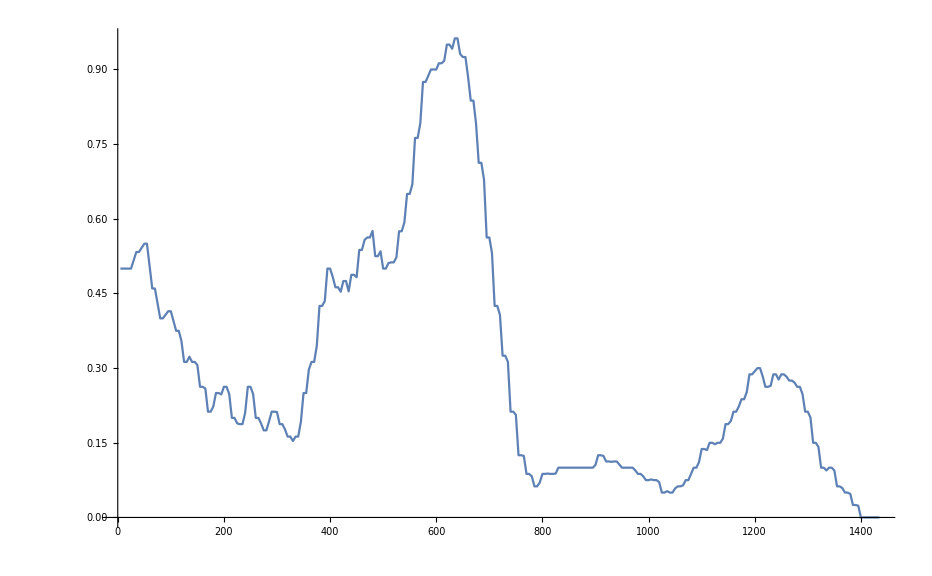

```mathematica
ListPlot[gasConsumptionSmoothedInterpolated,Joined->{True,True}]
```

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
```

```mathematica
precedingDay="2023-11-26"
```

2023-11-26

```mathematica
day="2023-11-27"
```

2023-11-27

```mathematica
precedingDayFormattedDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\formatted\\"<>precedingDay];
precedingDayFormattedDataFiles//Column
```

C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\external_temp.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\gas_flow.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\gas_stock.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\heat_flow.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\heating_state.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\heat_stock.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_1_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_2_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_3_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_4_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_5_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_6_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_7_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_8_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\formatted\2023-11-26\room_9_temps.csv

```mathematica
dayFormattedDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\formatted\\"<>day];
```

```mathematica
dayRawDataFiles=FileNames[All,"C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\raw\\"<>day];
dayRawDataFiles//Column
```

C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\albatros_state.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\external_temp.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\gas_pulse_times.txt
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\heatmeter_images
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\heatmeter_readouts.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\measured_temps.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\pump_states.csv
C:\Users\Beno\Documents\SZAKI\kazankontroll-dashboard\data\raw\2023-11-27\set_temps.csv

```mathematica
heatmeterReadoutsRaw=Map[
Flatten[{60ToExpression[StringSplit[#[[1]],":"][[1]]]+ToExpression[StringSplit[#[[1]],":"][[2]]],#[[2;;5]]}]
&,Import[dayRawDataFiles[[5]]]];
```

```mathematica
groundTruth={4340,1872,416,47}
```

{4340,1872,416,47}

```mathematica
cycle=1;
```

```mathematica
cycleReadouts=Transpose[Transpose[heatmeterReadoutsRaw][[{1,cycle+1}]]]
```

{{0,4340},{15,6862},{30,6862},{45,5337},{60,6860},{75,4340},{90,5337},{105,4340},{120,5337},{135,5337},{150,6862},{165,4340},{180,4340},{195,4340},{210,4340},{225,4340},{240,5337},{255,4340},{270,6n62},{285,6862},{300,6860},{315,4340},{330,5337},{345,5337},{360,6862},{702,4340},{720,5337},{735,4348},{750,4350},{765,5337},{780,5337},{795,4358},{810,4360},{825,4364},{840,3337},{870,4370},{885,4372},{900,5337},{915,5337},{930,4382},{945,4383},{960,4385},{975,5337},{990,4390},{1005,5337},{1020,4396},{1035,4399},{1050,3337},{1065,4404},{1080,5337},{1095,4403},{1110,4411},{1125,3337},{1140,4417},{1155,4419},{1170,4422},{1185,3337},{1200,3337},{1215,3337},{1230,3337},{1245,3337},{1260,4437},{1275,4439},{1305,4444},{1320,3337},{1335,4449},{1350,4452},{1365,4454},{1380,4456},{1395,3337},{1410,4457},{1425,5337}}

```mathematica
(*
- valamekkora súlyozott memória?
- nem a karakterenkénti különbséget kell nézni!
*)
```

```mathematica
60({5,0,0,1}-{4,9,9,9}){1000,100,10,1}/{5,5,5,5}
```

{12000,-10800,-1080,-96}

```mathematica
groundTruthChars=ToExpression[Flatten[{ConstantArray[0,4-Length[StringSplit[ToString[Round[groundTruth[[cycle]]]],""]]],StringSplit[ToString[Round[groundTruth[[cycle]]]],""]}]];
groundTruthTimeForChars={-5,-5,-5,-5};
powerThreshold={20,0,0,0.1};
cycleReadoutsValidReadingFilteredPowerFiltered=Quiet[Table[
time=cycleReadouts[[n]][[1]];
readout=cycleReadouts[[n]][[2]];
readoutChars=ToExpression[StringSplit[ToString[readout],""]];
powerRaw=60(readoutChars-groundTruthChars){1000,100,10,1}/(time-groundTruthTimeForChars);
oldGroundTruth=StringRiffle[Map[ToString,groundTruthChars],""];
oldGroundTruthTimeForChars=groundTruthTimeForChars;
Table[
If[
0<=powerRaw[[pos]]<powerThreshold[[cycle]],
{
groundTruthChars[[pos]]=readoutChars[[pos]],
groundTruthTimeForChars[[pos]]=time
},
Nothing
],
{pos,1,4}];
powerCorrected=60(readoutChars-groundTruthChars){1000,100,10,1}/(time-groundTruthTimeForChars);
newGroundTruth=StringRiffle[Map[ToString,groundTruthChars],""];
newGroundTruthTimeForChars=groundTruthTimeForChars;
{
time,
Row[oldGroundTruthTimeForChars],
oldGroundTruth,
readout,
newGroundTruth,
Grid[Transpose[Map[{#,Boole[0<=#<powerThreshold[[cycle]]]}&,powerRaw]]]
}//N
,{n,1,Length[cycleReadouts]}]]//Grid
```

0. | -5.-5.-5.-5. | 4340 | 4340. | 4340 | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1.
15. | 0.0.0.0. | 4340 | 6862. | 4342 | 8000. | 2000. | 80. | 8.
0. | 0. | 0. | 1.
30. | 0.0.0.15. | 4342 | 6862. | 4342 | 4000. | 1000. | 40. | 0.
0. | 0. | 0. | 1.
45. | 0.0.0.30. | 4342 | 5337. | 4342 | 1333.33 | 0. | -13.3333 | 20.
0. | 1. | 0. | 0.
60. | 0.45.0.30. | 4342 | 6860. | 4342 | 2000. | 2000. | 20. | -4.
0. | 0. | 0. | 0.
75. | 0.45.0.30. | 4342 | 4340. | 4342 | 0. | 0. | 0. | -2.66667
1. | 1. | 1. | 0.
90. | 75.75.75.30. | 4342 | 5337. | 4347 | 4000. | 0. | -40. | 5.
0. | 1. | 0. | 1.
105. | 75.90.75.90. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -28.
1. | 1. | 1. | 0.
120. | 105.105.105.90. | 4347 | 5337. | 4347 | 4000. | 0. | -40. | 0.
0. | 1. | 0. | 1.
135. | 105.120.105.120. | 4347 | 5337. | 4347 | 2000. | 0. | -20. | 0.
0. | 1. | 0. | 1.
150. | 105.135.105.135. | 4347 | 6862. | 4347 | 2666.67 | 2000. | 26.6667 | -20.
0. | 0. | 0. | 0.
165. | 105.135.105.135. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -14.
1. | 1. | 1. | 0.
180. | 165.165.165.135. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -9.33333
1. | 1. | 1. | 0.
195. | 180.180.180.135. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -7.
1. | 1. | 1. | 0.
210. | 195.195.195.135. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -5.6
1. | 1. | 1. | 0.
225. | 210.210.210.135. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -4.66667
1. | 1. | 1. | 0.
240. | 225.225.225.135. | 4347 | 5337. | 4347 | 4000. | 0. | -40. | 0.
0. | 1. | 0. | 1.
255. | 225.240.225.240. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -28.
1. | 1. | 1. | 0.
270. | 255.255.255.240. | 4347 | 6n62 | 4347 | 8000. | 6400. | 80. | -10.
0. | 0. | 0. | 0.
285. | 255.255.255.240. | 4347 | 6862. | 4347 | 4000. | 1000. | 40. | -6.66667
0. | 0. | 0. | 0.
300. | 255.255.255.240. | 4347 | 6860. | 4347 | 2666.67 | 666.667 | 26.6667 | -7.
0. | 0. | 0. | 0.
315. | 255.255.255.240. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -5.6
1. | 1. | 1. | 0.
330. | 315.315.315.240. | 4347 | 5337. | 4347 | 4000. | 0. | -40. | 0.
0. | 1. | 0. | 1.
345. | 315.330.315.330. | 4347 | 5337. | 4347 | 2000. | 0. | -20. | 0.
0. | 1. | 0. | 1.
360. | 315.345.315.345. | 4347 | 6862. | 4347 | 2666.67 | 2000. | 26.6667 | -20.
0. | 0. | 0. | 0.
702. | 315.345.315.345. | 4347 | 4340. | 4347 | 0. | 0. | 0. | -1.17647
1. | 1. | 1. | 0.
720. | 702.702.702.345. | 4347 | 5337. | 4347 | 3333.33 | 0. | -33.3333 | 0.
0. | 1. | 0. | 1.
735. | 702.720.702.720. | 4347 | 4348. | 4348 | 0. | 0. | 0. | 4.
1. | 1. | 1. | 1.
750. | 735.735.735.735. | 4348 | 4350. | 4348 | 0. | 0. | 40. | -32.
1. | 1. | 0. | 0.
765. | 750.750.735.735. | 4348 | 5337. | 4348 | 4000. | 0. | -20. | -2.
0. | 1. | 0. | 0.
780. | 750.765.735.735. | 4348 | 5337. | 4348 | 2000. | 0. | -13.3333 | -1.33333
0. | 1. | 0. | 0.
795. | 750.780.735.735. | 4348 | 4358. | 4358 | 0. | 0. | 10. | 0.
1. | 1. | 1. | 1.
810. | 795.795.795.795. | 4358 | 4360. | 4358 | 0. | 0. | 40. | -32.
1. | 1. | 0. | 0.
825. | 810.810.795.795. | 4358 | 4364. | 4358 | 0. | 0. | 20. | -8.
1. | 1. | 0. | 0.
840. | 825.825.795.795. | 4358 | 3337. | 4358 | -4000. | 0. | -26.6667 | -1.33333
0. | 1. | 0. | 0.
870. | 825.840.795.795. | 4358 | 4370. | 4378 | 0. | 0. | 16. | -6.4
1. | 1. | 1. | 0.
885. | 870.870.870.795. | 4378 | 4372. | 4378 | 0. | 0. | 0. | -4.
1. | 1. | 1. | 0.
900. | 885.885.885.795. | 4378 | 5337. | 4378 | 4000. | 0. | -160. | -0.571429
0. | 1. | 0. | 0.
915. | 885.900.885.795. | 4378 | 5337. | 4378 | 2000. | 0. | -80. | -0.5
0. | 1. | 0. | 0.
930. | 885.915.885.795. | 4378 | 4382. | 4388 | 0. | 0. | 13.3333 | -2.66667
1. | 1. | 1. | 0.
945. | 930.930.930.795. | 4388 | 4383. | 4388 | 0. | 0. | 0. | -2.
1. | 1. | 1. | 0.
960. | 945.945.945.795. | 4388 | 4385. | 4388 | 0. | 0. | 0. | -1.09091
1. | 1. | 1. | 0.
975. | 960.960.960.795. | 4388 | 5337. | 4388 | 4000. | 0. | -200. | -0.333333
0. | 1. | 0. | 0.
990. | 960.975.960.795. | 4388 | 4390. | 4388 | 0. | 0. | 20. | -2.46154
1. | 1. | 0. | 0.
1005. | 990.990.960.795. | 4388 | 5337. | 4388 | 4000. | 0. | -66.6667 | -0.285714
0. | 1. | 0. | 0.
1020. | 990.1005.960.795. | 4388 | 4396. | 4398 | 0. | 0. | 10. | -0.533333
1. | 1. | 1. | 0.
1035. | 1020.1020.1020.795. | 4398 | 4399. | 4399 | 0. | 0. | 0. | 0.25
1. | 1. | 1. | 1.
1050. | 1035.1035.1035.1035. | 4399 | 3337. | 4399 | -4000. | 0. | -240. | -8.
0. | 1. | 0. | 0.
1065. | 1035.1050.1035.1035. | 4399 | 4404. | 4399 | 0. | 400. | -180. | -10.
1. | 0. | 0. | 0.
1080. | 1065.1050.1035.1035. | 4399 | 5337. | 4399 | 4000. | 0. | -80. | -2.66667
0. | 1. | 0. | 0.
1095. | 1065.1080.1035.1035. | 4399 | 4403. | 4399 | 0. | 400. | -90. | -6.
1. | 0. | 0. | 0.
1110. | 1095.1080.1035.1035. | 4399 | 4411. | 4399 | 0. | 200. | -64. | -6.4
1. | 0. | 0. | 0.
1125. | 1110.1080.1035.1035. | 4399 | 3337. | 4399 | -4000. | 0. | -40. | -1.33333
0. | 1. | 0. | 0.
1140. | 1110.1125.1035.1035. | 4399 | 4417. | 4399 | 0. | 400. | -45.7143 | -1.14286
1. | 0. | 0. | 0.
1155. | 1140.1125.1035.1035. | 4399 | 4419. | 4399 | 0. | 200. | -40. | 0.
1. | 0. | 0. | 1.
1170. | 1155.1125.1035.1155. | 4399 | 4422. | 4399 | 0. | 133.333 | -31.1111 | -28.
1. | 0. | 0. | 0.
1185. | 1170.1125.1035.1155. | 4399 | 3337. | 4399 | -4000. | 0. | -24. | -4.
0. | 1. | 0. | 0.
1200. | 1170.1185.1035.1155. | 4399 | 3337. | 4399 | -2000. | 0. | -21.8182 | -2.66667
0. | 1. | 0. | 0.
1215. | 1170.1200.1035.1155. | 4399 | 3337. | 4399 | -1333.33 | 0. | -20. | -2.
0. | 1. | 0. | 0.
1230. | 1170.1215.1035.1155. | 4399 | 3337. | 4399 | -1000. | 0. | -18.4615 | -1.6
0. | 1. | 0. | 0.
1245. | 1170.1230.1035.1155. | 4399 | 3337. | 4399 | -800. | 0. | -17.1429 | -1.33333
0. | 1. | 0. | 0.
1260. | 1170.1245.1035.1155. | 4399 | 4437. | 4399 | 0. | 400. | -16. | -1.14286
1. | 0. | 0. | 0.
1275. | 1260.1245.1035.1155. | 4399 | 4439. | 4399 | 0. | 200. | -15. | 0.
1. | 0. | 0. | 1.
1305. | 1275.1245.1035.1275. | 4399 | 4444. | 4399 | 0. | 100. | -11.1111 | -10.
1. | 0. | 0. | 0.
1320. | 1305.1245.1035.1275. | 4399 | 3337. | 4399 | -4000. | 0. | -12.6316 | -2.66667
0. | 1. | 0. | 0.
1335. | 1305.1320.1035.1275. | 4399 | 4449. | 4399 | 0. | 400. | -10. | 0.
1. | 0. | 0. | 1.
1350. | 1335.1320.1035.1335. | 4399 | 4452. | 4399 | 0. | 200. | -7.61905 | -28.
1. | 0. | 0. | 0.
1365. | 1350.1320.1035.1335. | 4399 | 4454. | 4399 | 0. | 133.333 | -7.27273 | -10.
1. | 0. | 0. | 0.
1380. | 1365.1320.1035.1335. | 4399 | 4456. | 4399 | 0. | 100. | -6.95652 | -4.
1. | 0. | 0. | 0.
1395. | 1380.1320.1035.1335. | 4399 | 3337. | 4399 | -4000. | 0. | -10. | -2.
0. | 1. | 0. | 0.
1410. | 1380.1395.1035.1335. | 4399 | 4457. | 4399 | 0. | 400. | -6.4 | -1.6
1. | 0. | 0. | 0.
1425. | 1410.1395.1035.1335. | 4399 | 5337. | 4399 | 4000. | 0. | -9.23077 | -1.33333
0. | 1. | 0. | 0.

```mathematica
ListPlot[cycleReadoutsValidReadingFilteredPowerFiltered]
```

ListPlot::lpn: Grid[{{0.,{-5.,-5.,-5.,-5.},0047,3847.,0047,{{36000.,0.},{9600.,0.},{0.,0.},{0.,0.}}},{15.,{-5.,-5.,-5.,-5.},0047,8847.,0047,{{24000.,0.},{2400.,0.},{0.,0.},{0.,0.}}},{30.,{-5.,-5.,-5.,-5.},0047,3847.,0047,{{5142.86,0.},{1371.43,0.},{0.,0.},{0.,0.}}},{45.,{-5.,-5.,-5.,-5.},0047,1847.,0047,{{1200.,0.},{960.,0.},{0.,0.},{0.,0.}}},«4»,{120.,{-5.,-5.,-5.,-5.},0047,8847.,0047,{{3840.,0.},{384.,0.},{0.,0.},{0.,0.}}},{135.,{-5.,-5.,-5.,-5.},0047,8847.,0047,{{3428.57,0.},{342.857,0.},{0.,0.},{0.,0.}}},«62»}] is not a list of numbers or pairs of numbers.

ListPlot[0. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{36000.,0.},{9600.,0.},{0.,0.},{0.,0.}}
15. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{24000.,0.},{2400.,0.},{0.,0.},{0.,0.}}
30. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{5142.86,0.},{1371.43,0.},{0.,0.},{0.,0.}}
45. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{1200.,0.},{960.,0.},{0.,0.},{0.,0.}}
60. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{923.077,0.},{738.462,0.},{0.,0.},{0.,0.}}
75. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{750.,0.},{600.,0.},{0.,0.},{0.,0.}}
90. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{631.579,0.},{505.263,0.},{0.,0.},{0.,0.}}
105. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{1636.36,0.},{436.364,0.},{0.,0.},{0.,0.}}
120. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{3840.,0.},{384.,0.},{0.,0.},{0.,0.}}
135. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{3428.57,0.},{342.857,0.},{0.,0.},{0.,0.}}
150. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{3096.77,0.},{309.677,0.},{0.,0.},{0.,0.}}
165. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{352.941,0.},{282.353,0.},{0.,0.},{0.,0.}}
180. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{324.324,0.},{259.459,0.},{0.,0.},{0.,0.}}
195. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{2400.,0.},{240.,0.},{0.,0.},{0.,0.}}
210. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{2232.56,0.},{223.256,0.},{0.,0.},{0.,0.}}
225. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{2086.96,0.},{208.696,0.},{0.,0.},{0.,0.}}
240. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{1959.18,0.},{195.918,0.},{0.,0.},{0.,0.}}
255. | {-5.,-5.,-5.,-5.} | 0047 | n860 | 0047 | {{4153.85,0.},{184.615,0.},{4.61538,0.},{-1.61538,0.}}
270. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{218.182,0.},{174.545,0.},{0.,0.},{0.,0.}}
285. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{206.897,0.},{165.517,0.},{0.,0.},{0.,0.}}
300. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{1573.77,0.},{157.377,0.},{0.,0.},{0.,0.}}
315. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{187.5,0.},{150.,0.},{0.,0.},{0.,0.}}
330. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{1432.84,0.},{143.284,0.},{0.,0.},{0.,0.}}
345. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{1371.43,0.},{137.143,0.},{0.,0.},{0.,0.}}
360. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{164.384,0.},{131.507,0.},{0.,0.},{0.,0.}}
702. | {-5.,-5.,-5.,-5.} | 0047 | n860 | 0047 | {{2206.51,0.},{67.8925,0.},{1.69731,0.},{-0.594059,0.}}
720. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{248.276,0.},{66.2069,0.},{0.,0.},{0.,0.}}
735. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{648.649,0.},{64.8649,0.},{0.,0.},{0.,0.}}
750. | {-5.,-5.,-5.,-5.} | 0047 | n860 | 0047 | {{2304.64,0.},{63.5762,0.},{1.5894,0.},{-0.556291,0.}}
765. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{233.766,0.},{62.3377,0.},{0.,0.},{0.,0.}}
780. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{229.299,0.},{61.1465,0.},{0.,0.},{0.,0.}}
795. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{600.,0.},{60.,0.},{0.,0.},{0.,0.}}
810. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{73.6196,0.},{58.8957,0.},{0.,0.},{0.,0.}}
825. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{578.313,0.},{57.8313,0.},{0.,0.},{0.,0.}}
840. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{213.018,0.},{56.8047,0.},{0.,0.},{0.,0.}}
870. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{68.5714,0.},{54.8571,0.},{0.,0.},{0.,0.}}
885. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{202.247,0.},{53.9326,0.},{0.,0.},{0.,0.}}
900. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{530.387,0.},{53.0387,0.},{0.,0.},{0.,0.}}
915. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{65.2174,0.},{52.1739,0.},{0.,0.},{0.,0.}}
930. | {-5.,-5.,-5.,-5.} | 0047 | 1887. | 0047 | {{64.1711,0.},{51.3369,0.},{2.56684,0.},{0.,0.}}
945. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{63.1579,0.},{50.5263,0.},{0.,0.},{0.,0.}}
960. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{497.409,0.},{49.7409,0.},{0.,0.},{0.,0.}}
975. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{183.673,0.},{48.9796,0.},{0.,0.},{0.,0.}}
990. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{60.3015,0.},{48.2412,0.},{0.,0.},{0.,0.}}
1005. | {-5.,-5.,-5.,-5.} | 0047 | 3847. | 0047 | {{178.218,0.},{47.5248,0.},{0.,0.},{0.,0.}}
1020. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{58.5366,0.},{46.8293,0.},{0.,0.},{0.,0.}}
1035. | {-5.,-5.,-5.,-5.} | 0047 | 8847. | 0047 | {{461.538,0.},{46.1538,0.},{0.,0.},{0.,0.}}
1050. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{56.872,0.},{45.4976,0.},{0.,0.},{0.,0.}}
1065. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{56.0748,0.},{44.8598,0.},{0.,0.},{0.,0.}}
1080. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{55.2995,0.},{44.2396,0.},{0.,0.},{0.,0.}}
1095. | {-5.,-5.,-5.,-5.} | 0047 | 3849. | 0047 | {{163.636,0.},{43.6364,0.},{0.,0.},{0.109091,0.}}
1110. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{53.8117,0.},{43.0493,0.},{0.,0.},{0.,0.}}
1125. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{53.0973,0.},{42.4779,0.},{0.,0.},{0.,0.}}
1140. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{52.4017,0.},{41.9214,0.},{0.,0.},{0.,0.}}
1155. | {-5.,-5.,-5.,-5.} | 0047 | 3862. | 0047 | {{155.172,0.},{41.3793,0.},{1.03448,0.},{-0.258621,0.}}
1170. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{51.0638,0.},{40.8511,0.},{0.,0.},{0.,0.}}
1185. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{50.4202,0.},{40.3361,0.},{0.,0.},{0.,0.}}
1200. | {-5.,-5.,-5.,-5.} | 0047 | 8871. | 0047 | {{398.34,0.},{39.834,0.},{1.49378,0.},{-0.298755,0.}}
1215. | {-5.,-5.,-5.,-5.} | 0047 | 3874. | 0047 | {{147.541,0.},{39.3443,0.},{1.47541,0.},{-0.147541,0.}}
1230. | {-5.,-5.,-5.,-5.} | 0047 | 3877. | 0047 | {{145.749,0.},{38.8664,0.},{1.45749,0.},{0.,0.}}
1245. | {-5.,-5.,-5.,-5.} | 0047 | 2880. | 0047 | {{96.,0.},{38.4,0.},{1.92,0.},{-0.336,0.}}
1260. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{47.4308,0.},{37.9447,0.},{0.,0.},{0.,0.}}
1275. | {-5.,-5.,-5.,-5.} | 0047 | 3886. | 0047 | {{140.625,0.},{37.5,0.},{1.875,0.},{-0.046875,0.}}
1305. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{45.8015,0.},{36.6412,0.},{0.,0.},{0.,0.}}
1320. | {-5.,-5.,-5.,-5.} | 0047 | 8894. | 0047 | {{362.264,0.},{36.2264,0.},{2.26415,0.},{-0.135849,0.}}
1335. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{44.7761,0.},{35.8209,0.},{0.,0.},{0.,0.}}
1350. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{44.2804,0.},{35.4244,0.},{0.,0.},{0.,0.}}
1365. | {-5.,-5.,-5.,-5.} | 0047 | 1847. | 0047 | {{43.7956,0.},{35.0365,0.},{0.,0.},{0.,0.}}
1380. | {-5.,-5.,-5.,-5.} | 0047 | 1848. | 0048 | {{43.3213,0.},{34.657,0.},{0.,0.},{0.0433213,1.}}
1395. | {-5.,-5.,-5.,1380.} | 0048 | 3898. | 0048 | {{128.571,0.},{34.2857,0.},{2.14286,0.},{0.,0.}}
1410. | {-5.,-5.,-5.,1380.} | 0048 | 3898. | 0048 | {{127.208,0.},{33.9223,0.},{2.12014,0.},{0.,0.}}
1425. | {-5.,-5.,-5.,1380.} | 0048 | 1848. | 0048 | {{41.958,0.},{33.5664,0.},{0.,0.},{0.,0.}}]

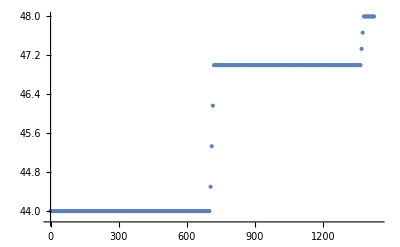

```mathematica
minuteStep=5;
cycleReadoutsValidReadingFilteredPowerFilteredInterpolated=Select[Quiet[Table[
precedingPos=PrecedingPos[Transpose[cycleReadoutsValidReadingFilteredPowerFiltered][[1]],minute];
precedingTime=cycleReadoutsValidReadingFilteredPowerFiltered[[precedingPos]][[1]];
precedingReading=cycleReadoutsValidReadingFilteredPowerFiltered[[precedingPos]][[2]];
succeedingTime=cycleReadoutsValidReadingFilteredPowerFiltered[[precedingPos+1]][[1]];
succeedingReading=cycleReadoutsValidReadingFilteredPowerFiltered[[precedingPos+1]][[2]];
{
precedingTime(1-((minute-precedingTime)/(succeedingTime-precedingTime)))+succeedingTime((minute-precedingTime)/(succeedingTime-precedingTime)),
precedingReading(1-((minute-precedingTime)/(succeedingTime-precedingTime)))+succeedingReading((minute-precedingTime)/(succeedingTime-precedingTime))
}//N
,{minute,0,24 60,minuteStep}]],NumberQ[Total[#]]&];ListPlot[cycleReadoutsValidReadingFilteredPowerFilteredInterpolated,PlotRange->{{0,24 60},All}]
```

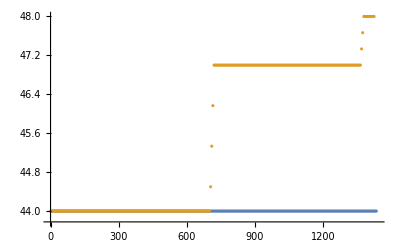

```mathematica
ListPlot[
{
Transpose[Transpose[Import[dayFormattedDataFiles[[6]]]][[{1,cycle+1}]]],
cycleReadoutsValidReadingFilteredPowerFilteredInterpolated
},PlotRange->{{0,24 60},All}
]
```

```mathematica
Differences[Transpose[Transpose[Transpose[Import[dayFormattedDataFiles[[6]]]][[{1,cycle+1}]]]][[2]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.727,1.212,1.213,1.212,1.212,1.212,1.212,0.667,0.666,0.667,0.889,0.889,0.889,0.889,0.888,0.889,0.889,0.889,0.889,0.667,0.666,0.667,1.333,1.334,1.333,0.667,0.666,0.667,0.667,0.666,0.667,0.667,0.666,0.667,0.667,0.666,0.667,1.111,1.111,1.111,1.111,1.112,1.111,1.111,1.111,1.111,0.333,0.334,0.333,0.667,0.666,0.667,0.833,0.834,0.833,0.833,0.834,0.833,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.889,0.889,0.889,0.889,0.888,0.889,0.889,0.889,0.889,1.,1.,1.,-180.833,-180.834,-180.833,-180.833,-180.834,-180.833,0.,0.,0.,0.,0.,0.,0.,0.,0.,183.667,183.666,183.667,183.667,183.666,183.667,0.833,0.834,0.833,0.833,0.834,0.833,0.889,0.889,0.889,0.889,0.888,0.889,0.889,0.889,0.889,0.667,0.666,0.667,0.667,0.666,0.667,0.,0,0,0,0,0,0,0,0,0,0}

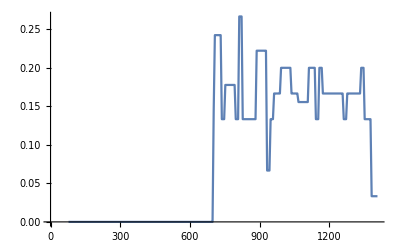

```mathematica
timeStep=5;
cyclePower=Select[Quiet[Table[
precedingPos=PrecedingPos[Transpose[cycleReadoutsValidReadingFilteredPowerFilteredInterpolated][[1]],time];
precedingTime=cycleReadoutsValidReadingFilteredPowerFilteredInterpolated[[precedingPos]][[1]];
precedingReading=cycleReadoutsValidReadingFilteredPowerFilteredInterpolated[[precedingPos]][[2]];
succeedingTime=cycleReadoutsValidReadingFilteredPowerFilteredInterpolated[[precedingPos+1]][[1]];
succeedingReading=cycleReadoutsValidReadingFilteredPowerFilteredInterpolated[[precedingPos+1]][[2]];
{
(succeedingTime+precedingTime)/2,
(succeedingReading-precedingReading)/(succeedingTime-precedingTime)
}
,{time,0,24 60-timeStep,timeStep}]],NumberQ[Total[#]]&&0<=#[[2]]&];
ListPlot[
cyclePower,Joined->True
]
```

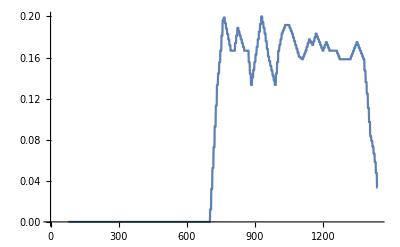

```mathematica
powerSmoothWindow= 60;
cyclePowerSmoothed=Select[Quiet[Table[
{time,Mean[Select[cyclePower,Between[#[[1]],{time-powerSmoothWindow,time}]&]][[2]]}
,{time,0,24 60}]],NumberQ[Total[#]]&];
ListPlot[cyclePowerSmoothed,Joined->True]
```

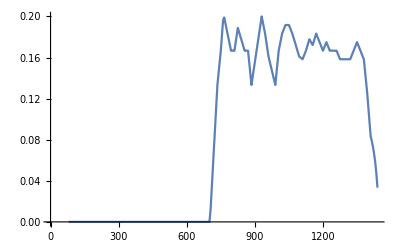

```mathematica
minuteStep=5;
cyclePowerSmoothedInterpolated=Select[Quiet[Table[
precedingPos=PrecedingPos[Transpose[cyclePowerSmoothed][[1]],minute];
precedingTime=cyclePowerSmoothed[[precedingPos]][[1]];
precedingReading=cyclePowerSmoothed[[precedingPos]][[2]];
succeedingTime=cyclePowerSmoothed[[precedingPos+1]][[1]];
succeedingReading=cyclePowerSmoothed[[precedingPos+1]][[2]];
{
precedingTime(1-((minute-precedingTime)/(succeedingTime-precedingTime)))+succeedingTime((minute-precedingTime)/(succeedingTime-precedingTime)),
precedingReading(1-((minute-precedingTime)/(succeedingTime-precedingTime)))+succeedingReading((minute-precedingTime)/(succeedingTime-precedingTime))
}//N
,{minute,0,24 60,minuteStep}]],NumberQ[Total[#]]&];
ListPlot[cyclePowerSmoothedInterpolated,Joined->True]
```

```mathematica
newGroundTruth=cycleReadoutsValidReadingFilteredPowerFilteredInterpolated[[-1]][[2]]
```

4457.

```mathematica
ListPlot[
{
,
cycleReadoutsValidReadingFilteredPowerFilteredInterpolated
},PlotRange->{{0,24 60},All}
]
```

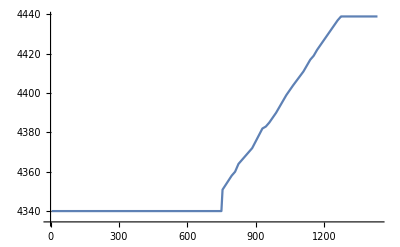
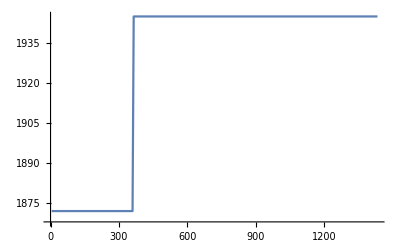
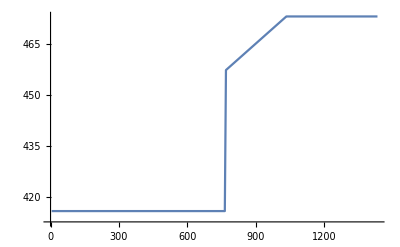
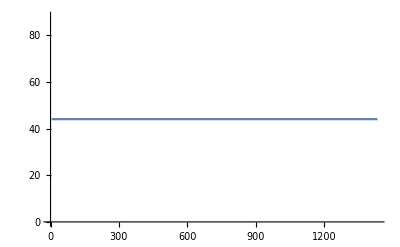

```mathematica
Table[
ListPlot[Transpose[Transpose[Import["C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\formatted\\2023-11-27\\heat_stock.csv"]][[{1,cycle+1}]]],Joined->True]
,{cycle,1,4}]
```

```mathematica
Transpose[Transpose[Import["C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\formatted\\2023-11-27\\heat_stock.csv"]][[{1,4+1}]]]
```

{{5,44.},{10,44.},{15,44.},{20,44.},{25,44.},{30,44.},{35,44.},{40,44.},{45,44.},{50,44.},{55,44.},{60,44.},{65,44.},{70,44.},{75,44.},{80,44.},{85,44.},{90,44.},{95,44.},{100,44.},{105,44.},{110,44.},{115,44.},{120,44.},{125,44.},{130,44.},{135,44.},{140,44.},{145,44.},{150,44.},{155,44.},{160,44.},{165,44.},{170,44.},{175,44.},{180,44.},{185,44.},{190,44.},{195,44.},{200,44.},{205,44.},{210,44.},{215,44.},{220,44.},{225,44.},{230,44.},{235,44.},{240,44.},{245,44.},{250,44.},{255,44.},{260,44.},{265,44.},{270,44.},{275,44.},{280,44.},{285,44.},{290,44.},{295,44.},{300,44.},{305,44.},{310,44.},{315,44.},{320,44.},{325,44.},{330,44.},{335,44.},{340,44.},{345,44.},{350,44.},{355,44.},{360,44.},{365,44.},{370,44.},{375,44.},{380,44.},{385,44.},{390,44.},{395,44.},{400,44.},{405,44.},{410,44.},{415,44.},{420,44.},{425,44.},{430,44.},{435,44.},{440,44.},{445,44.},{450,44.},{455,44.},{460,44.},{465,44.},{470,44.},{475,44.},{480,44.},{485,44.},{490,44.},{495,44.},{500,44.},{505,44.},{510,44.},{515,44.},{520,44.},{525,44.},{530,44.},{535,44.},{540,44.},{545,44.},{550,44.},{555,44.},{560,44.},{565,44.},{570,44.},{575,44.},{580,44.},{585,44.},{590,44.},{595,44.},{600,44.},{605,44.},{610,44.},{615,44.},{620,44.},{625,44.},{630,44.},{635,44.},{640,44.},{645,44.},{650,44.},{655,44.},{660,44.},{665,44.},{670,44.},{675,44.},{680,44.},{685,44.},{690,44.},{695,44.},{700,44.},{705,44.},{710,44.},{715,44.},{720,44.},{725,44.},{730,44.},{735,44.},{740,44.},{745,44.},{750,44.},{755,44.},{760,44.},{765,44.},{770,44.},{775,44.},{780,44.},{785,44.},{790,44.},{795,44.},{800,44.},{805,44.},{810,44.},{815,44.},{820,44.},{825,44.},{830,44.},{835,44.},{840,44.},{845,44.},{850,44.},{855,44.},{860,44.},{865,44.},{870,44.},{875,44.},{880,44.},{885,44.},{890,44.},{895,44.},{900,44.},{905,44.},{910,44.},{915,44.},{920,44.},{925,44.},{930,44.},{935,44.},{940,44.},{945,44.},{950,44.},{955,44.},{960,44.},{965,44.},{970,44.},{975,44.},{980,44.},{985,44.},{990,44.},{995,44.},{1000,44.},{1005,44.},{1010,44.},{1015,44.},{1020,44.},{1025,44.},{1030,44.},{1035,44.},{1040,44.},{1045,44.},{1050,44.},{1055,44.},{1060,44.},{1065,44.},{1070,44.},{1075,44.},{1080,44.},{1085,44.},{1090,44.},{1095,44.},{1100,44.},{1105,44.},{1110,44.},{1115,44.},{1120,44.},{1125,44.},{1130,44.},{1135,44.},{1140,44.},{1145,44.},{1150,44.},{1155,44.},{1160,44.},{1165,44.},{1170,44.},{1175,44.},{1180,44.},{1185,44.},{1190,44.},{1195,44.},{1200,44.},{1205,44.},{1210,44.},{1215,44.},{1220,44.},{1225,44.},{1230,44.},{1235,44.},{1240,44.},{1245,44.},{1250,44.},{1255,44.},{1260,44.},{1265,44.},{1270,44.},{1275,44.},{1280,44.},{1285,44.},{1290,44.},{1295,44.},{1300,44.},{1305,44.},{1310,44.},{1315,44.},{1320,44.},{1325,44.},{1330,44.},{1335,44.},{1340,44.},{1345,44.},{1350,44.},{1355,44.},{1360,44.},{1365,44.},{1370,44.},{1375,44.},{1380,44.},{1385,44.},{1390,44.},{1395,44.},{1400,44.},{1405,44.},{1410,44.},{1415,44.},{1420,44.},{1425,44.},{1430,44.},{1435,44.}}

## Bayesian heatmeter reader

### generate power prior

```mathematica
startDate={DateObject["2023-11-26 01:45"],DateObject["2023-11-26 01:45"],DateObject["2023-11-26 02:00"],DateObject["2023-11-26 02:30"]};
```

```mathematica
veridicalReadings=Map[
Map[#[[{1,3}]]&,#]
&,SortBy[GatherBy[Map[
{DateDifferenceInUnits[startDate[[ToExpression[#[[2]]]]],DateObject[#[[1]]],"Hour"],ToExpression[#[[2]]],ToExpression[#[[3]]]}
&,Map[
StringSplit[#,","]
&,StringSplit[Import["C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\services\\veridical_readings.txt"],"\n"]]],#[[2]]&],#[[2]][[2]]&]];
```

```mathematica
Position[Differences[veridicalReadings[[2]]],{5.716666666666669,78}]
```

{{48}}

```mathematica
veridicalReadings[[2]][[47;;51]]
```

{{27.75,1937},{28.25,1945},{33.9667,2023},{34.5,2033},{34.75,2036}}

```mathematica
Table[Reverse[Sort[
Select[Map[
#[[2]]/#[[1]]
&,Differences[veridicalReadings[[cycle]]]],0<#&]]],{cycle,1,4}]//N//Round//Grid
```

28 | 16 | 16 | 16 | 15 | 15 | 14 | 14 | 14 | 13 | 13 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 11 | 11 | 11 | 11 | 11 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 7 | 7 | 7 | 7 | 6 | 6 | 6 | 6 | 6 | 4 | 4 | 4 | 4 | 2 | 2 | 2 | 1 | 1 | 1
104 | 44 | 36 | 36 | 36 | 32 | 27 | 24 | 24 | 22 | 20 | 20 | 20 | 20 | 19 | 19 | 18 | 18 | 18 | 18 | 17 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 15 | 15 | 14 | 14 | 14 | 13 | 13 | 13 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 11 | 8 | 8 | 8 | 7 | 6 | 6 | 6 | 5 | 4 | 4 | 4 | 3 | 2 | 2 | 2 | 2 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
28 | 20 | 20 | 18 | 16 | 16 | 16 | 16 | 14 | 14 | 13 | 12 | 12 | 12 | 12 | 10 | 10 | 10 | 10 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 7 | 7 | 7 | 7 | 7 | 7 | 6 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
13 | 12 | 12 | 12 | 12 | 12 | 11 | 11 | 4 | 3 | 2 | 2 | 2 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
powerDistributions=Table[Select[Map[
#[[2]]/#[[1]]
&,Differences[veridicalReadings[[cycle]]]],0<#<45&],{cycle,1,4}];
```

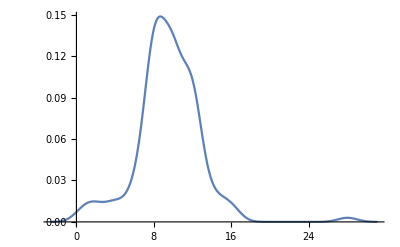
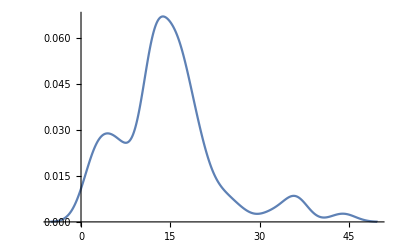
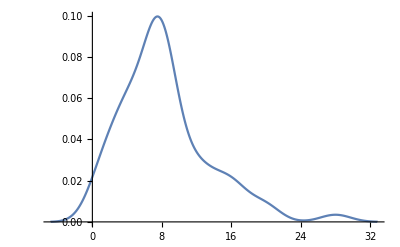
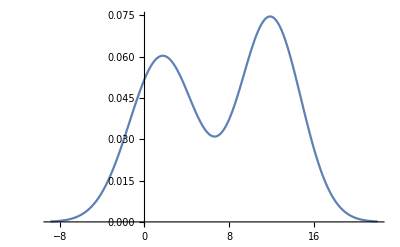

```mathematica
Table[SmoothHistogram[
powerDistributions[[cycle]],
PlotRange->{All,All}
],{cycle,1,4}]
```

```mathematica
PowerFunction[x]:=Evaluate[PDF[SmoothKernelDistribution[Flatten[powerDistributions],2],x]]
```

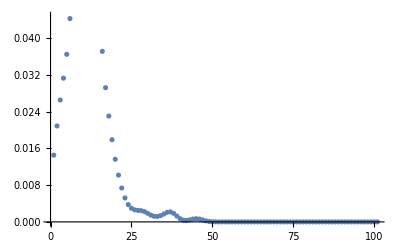

```mathematica
ListPlot[Table[
Evaluate[PowerFunction[x]]
,{x,0,100}]]
```

```mathematica
Show[{
Histogram[Flatten[powerDistributions],Automatic,"PDF",PlotRange->All],
(*Table[SmoothHistogram[powerDistributions[[cycle]],Automatic,"PDF",PlotRange->All,PlotStyle->Blue],{cycle,1,4}],*)
Plot[PDF[WeibullDistribution[alpha,beta,gamma],x],{x,0,Max[powerDistributions]},PlotStyle->{Red,Dashed}]
}],
{{alpha,3.2,"Shape"},0.1,10,0.1},
{{beta,10,"Scale"},0.1,20,0.1},
{{gamma,0.1,"Location"},0.1,10,0.1}
```

```mathematica
Evaluate[PDF[WeibullDistribution[1.8,13.9,0.1],x][[1]][[1]][[1]]]
```

0.0157705 ⅇ^(-0.0087614 (-0.1+x)^1.8) (-0.1+x)^0.8

### belief update

```mathematica
PowerWeightingFunctionHeatingOn[x_]:=0.01577051459395669 ⅇ^(-0.008761396996642606 (-0.1+(x+0.5))^1.8) (-0.1+x+0.5)^0.8
```

```mathematica
PowerWeightingFunctionHeatingOff[x_]:=Exp[-100 x]
```

```mathematica
PowerWeightingFunction[x_,h_]:=Quiet[Re[If[h==0,PowerWeightingFunctionHeatingOff[x],PowerWeightingFunctionHeatingOn[x]]]]
```

```mathematica
StateToEnergy[state_]:=ToExpression[StringRiffle[Map[ToString,state],""]]
```

```mathematica
EnergyToState[energy_]:=Map[ToExpression,StringSplit[ToString[Round[energy]],""]]//Flatten[{ConstantArray[0,4-Length[#]],#}]&
```

```mathematica
heatingState=Import["C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\formatted\\2023-11-27\\heating_state.csv"];
```

```mathematica
readouts=Table[Map[
{
ToExpression[StringTake[StringDrop[#,-2],{2,3}]]60+ToExpression[StringTake[StringDrop[#,-2],{4,5}]],
ToExpression[StringDrop[StringDrop[#,-2],6]][[1+4(cycle-1);;4(cycle)]]
}
&,Drop[Drop[StringSplit[Import["C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\services\\prob_readouts_mathematica_1.txt"],"\n"],1],-2]]
,{cycle,1,4}];
```

```mathematica
veridicalReadingsRealDates=Map[
Map[#[[{1,3}]]&,#]
&,SortBy[GatherBy[Map[
{DateObject[#[[1]]],ToExpression[#[[2]]],ToExpression[#[[3]]]}
&,Map[
StringSplit[#,","]
&,StringSplit[Import["C:\\Users\\Beno\\Documents\\SZAKI\\kazankontroll-dashboard\\data\\services\\veridical_readings.txt"],"\n"]]],#[[2]]&],#[[2]][[2]]&]];
```

```mathematica
truth=Table[Map[
{
DateValue[#[[1]],"Hour"]60+DateValue[#[[1]],"Minute"],
#[[2]]
}
&,Select[veridicalReadingsRealDates[[cycle]],DateValue[#[[1]],"Day"]==27&]
],{cycle,1,4}];
```

```mathematica
StartingPriorFunction[power_,groundTruth_]:=PDF[NormalDistribution[groundTruth,0.1],power];
```

```mathematica
powerMax=50;
prevPriorCutoff=0.005;
weightPrior=0;
weightTransition=2;
weightOCR=10;
```

```mathematica
cycle=2;
```

```mathematica
lastReadTime=-15;
prior=Flatten[Table[Table[Table[Table[
{{char1,char2,char3,char4},StartingPriorFunction[StateToEnergy[{char1,char2,char3,char4}],Transpose[Map[First,truth]][[2]][[cycle]]]}
,{char4,0,9}],{char3,0,9}],{char2,0,9}],{char1,0,9}],3];
bayesianReading=Table[
Module[
{time,elapsedTime,readout,inference},
```

```mathematica
timedReadout=Drop[readouts[[cycle]],1][[3]]
```

{60,{{0.,0.,0.,0.0526316,0.,0.,0.,0.,0.947368,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.}}}

```mathematica
time=timedReadout[[1]];
readout=timedReadout[[2]];
elapsedTime=N[(time-lastReadTime)/60];
```

```mathematica
inference=Module[
{heating,priorStatesWithEnoughProbability,firstPrevStateToBeConsidered,lastPrevStateToBeConsidered,posteriorUpdate,unnormalizedPosterior,normalizedPosterior},
```

```mathematica
heating=heatingState[[PrecedingPos[Transpose[heatingState][[1]],time]]][[cycle+1]];
priorStatesWithEnoughProbability=Select[prior,prevPriorCutoff<=#[[2]]&];
```

```mathematica
If[
priorStatesWithEnoughProbability!={},
firstPrevStateToBeConsidered=Round[StateToEnergy[First[priorStatesWithEnoughProbability][[1]]]-powerMax/elapsedTime];
lastPrevStateToBeConsidered=Round[StateToEnergy[Last[priorStatesWithEnoughProbability][[1]]]+powerMax/elapsedTime];
posteriorUpdate=Table[
Module[
{currentState,likelihoodOCR,previousStatesToBeConsidered,likelihoodTransition,priorOfCurrentState},
currentState=EnergyToState[currentStateEnergy];
likelihoodOCR=Total[Table[readout[[char]][[currentState[[char]]+1]],{char,1,4}]]/4;
previousStatesToBeConsidered=Select[prior[[Max[Round[currentStateEnergy-powerMax elapsedTime],1];;currentStateEnergy+1]],prevPriorCutoff<=#[[2]]&];
likelihoodTransition=Total[Table[
Module[
{previousState,previousStateP,power},
previousState=previousStatePrior[[1]];
previousStateP=previousStatePrior[[2]];
power=N[(StateToEnergy[currentState]-StateToEnergy[previousState])/elapsedTime];
previousStateP PowerWeightingFunction[power,heating]
]
,{previousStatePrior,previousStatesToBeConsidered}]];
priorOfCurrentState=prior[[currentStateEnergy+1]][[2]];
{
currentStateEnergy,
likelihoodOCR,
likelihoodTransition,
priorOfCurrentState,
 likelihoodOCR likelihoodTransition,
(weightPrior priorOfCurrentState+ weightTransition likelihoodTransition+ weightOCR likelihoodOCR)/(weightPrior+weightTransition+weightOCR)
}
],{currentStateEnergy,firstPrevStateToBeConsidered,lastPrevStateToBeConsidered}];
unnormalizedPosterior=Transpose[{Transpose[prior][[1]],Transpose[prior][[2]]0}];
Table[unnormalizedPosterior[[update[[1]]+1]]={EnergyToState[update[[1]]],update[[5]]},{update,posteriorUpdate}];
normalizedPosterior=Transpose[{Transpose[unnormalizedPosterior][[1]],Transpose[unnormalizedPosterior][[2]]/Total[Transpose[unnormalizedPosterior][[2]]]}];,
posteriorUpdate=None;
normalizedPosterior=prior;
];
 {normalizedPosterior,posteriorUpdate}
];
```

```mathematica
lastReadTime=time;
prior=inference[[1]]
```

{{{0,0,0,0},0.},{{0,0,0,1},0.},{{0,0,0,2},0.},{{0,0,0,3},0.},{{0,0,0,4},0.},{{0,0,0,5},0.},{{0,0,0,6},0.},{{0,0,0,7},0.},{{0,0,0,8},0.},{{0,0,0,9},0.},{{0,0,1,0},0.},{{0,0,1,1},0.},{{0,0,1,2},0.},{{0,0,1,3},0.},{{0,0,1,4},0.},{{0,0,1,5},0.},{{0,0,1,6},0.},{{0,0,1,7},0.},{{0,0,1,8},0.},{{0,0,1,9},0.},{{0,0,2,0},0.},{{0,0,2,1},0.},9956,{{9,9,7,8},0.},{{9,9,7,9},0.},{{9,9,8,0},0.},{{9,9,8,1},0.},{{9,9,8,2},0.},{{9,9,8,3},0.},{{9,9,8,4},0.},{{9,9,8,5},0.},{{9,9,8,6},0.},{{9,9,8,7},0.},{{9,9,8,8},0.},{{9,9,8,9},0.},{{9,9,9,0},0.},{{9,9,9,1},0.},{{9,9,9,2},0.},{{9,9,9,3},0.},{{9,9,9,4},0.},{{9,9,9,5},0.},{{9,9,9,6},0.},{{9,9,9,7},0.},{{9,9,9,8},0.},{{9,9,9,9},0.}}
 |  |  |  |

```mathematica
{time,prior,inference}
]
,{timedReadout,Drop[readouts[[cycle]],1]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

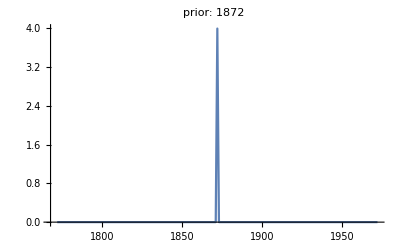
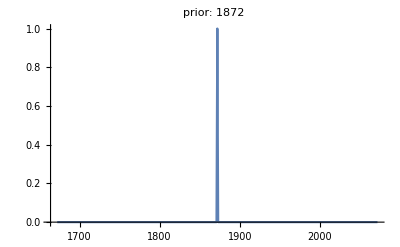
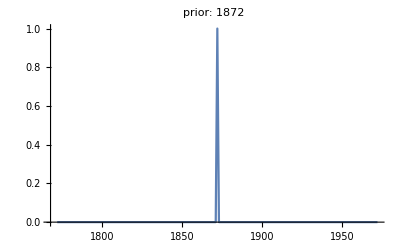
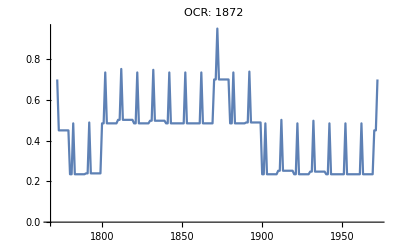
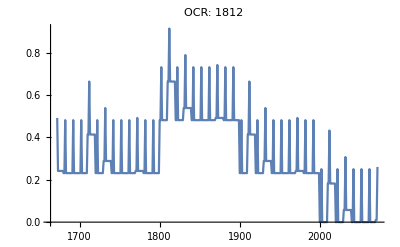
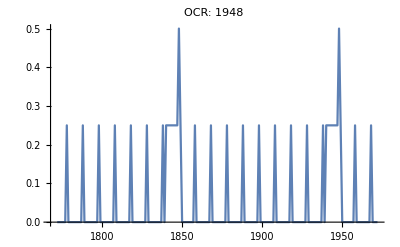
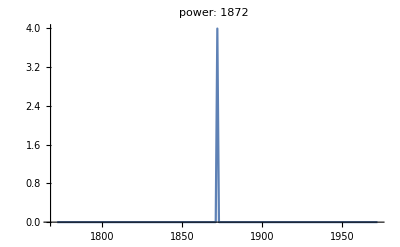
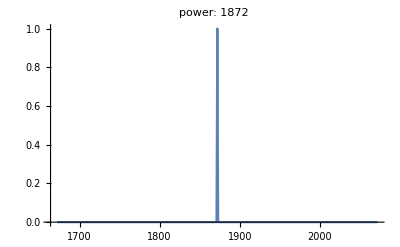
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
MAP | {0,15} | 1872
truth | {0,15} | 1872 | MAP | {0,30} | 1872
truth | {0,30} | 1872 | MAP | {1,0} | 1972
truth | {0,45} | 1872

```mathematica
Table[
MAP=Reverse[SortBy[Transpose[Transpose[reading[[3]][[2]]][[{1,5}]]],Last]][[1]][[1]];
Join[
Table[
ListPlot[
Transpose[Transpose[reading[[3]][[2]]][[{1,val}]]],Joined->True,
PlotLabel->{
"OCR",
"power",
"prior",
"posterior"
}[[val-1]]<>": "<>ToString[First[Reverse[SortBy[Transpose[Transpose[reading[[3]][[2]]][[{1,val}]]],Last]]][[1]]],PlotRange->{All,All}
],{val,{4,2,3,5}}],
{
Grid[{
{"MAP",MinutesSinceMidnightToHourMinute[reading[[1]]],MAP},
truth[[cycle]][[Position[truth[[cycle]],Nearest[Transpose[truth[[cycle]]][[1]],reading[[1]]][[1]]][[1]][[1]]]]//{"truth",MinutesSinceMidnightToHourMinute[#[[1]]],#[[2]]}&
}]
}
]
,{reading,Select[
bayesianReading,
Length[#[[3]][[2]]]!=0&
]}]//Transpose//Grid
```